```mathematica
params ={m -> 1,b -> 1, a-> 5,g -> 9.8}
eqns = {(3/2+1/25)p1''[t]- (1/25+1/2)p2''[t] == ((1/2(p1[t]+p2[t])Cos[1/5(p2[t]-p1[t])]+1/2(p1'[t]+p2'[t]) Sin[1/5(p2[t]-p1[t])])Sin[1/5(p2[t]-p1[t])]+( Sin[1/5(p2[t]-p1[t])] 1/2(p1[t]+p2[t])- Cos[1/5(p2[t]-p1[t])] 1/2(p1'[t]+p2'[t])+10*Sin[Pi/3])Cos[1/5(p2[t]-p1[t])]),
(3/2+ 1/25)p2''[t]- (1/25+1/2)p1''[t] == -(( 1/2(p1[t]+p2[t])Cos[1/5(p2[t]-p1[t])]+1/2(p1'[t]+p2'[t]) Sin[1/5(p2[t]-p1[t])])Sin[1/5(p2[t]-p1[t])]-( Sin[1/5(p2[t]-p1[t])] 1/2(p1[t]+p2[t])- Cos[1/5(p2[t]-p1[t])] 1/2(p1'[t]+p2'[t])+10*Sin[Pi/3])Cos[1/5(p2[t]-p1[t])])}
ics = {p1[0]==-Pi/3, p2[0] == +Pi/5, p1'[0] == -1, p2'[0] == +1.5}
sol = NDSolve[{eqns,ics}/.params,{p1,p2},{t,0,100}]
theta = 1/5*(p2[t]-p1[t])
Plot[Evaluate[theta/.sol],{t,0,100}]
Plot[Evaluate[p1[t]/.sol],{t,0,100}]
Plot[Evaluate[p2[t]/.sol],{t,0,100}]
```

{m→1,b→1,a→5,g→9.8}

{(77 p1''[t])/50-(27 p2''[t])/50==Cos[1/5 (-p1[t]+p2[t])] (5 √3+1/2 (p1[t]+p2[t]) Sin[1/5 (-p1[t]+p2[t])]-1/2 Cos[1/5 (-p1[t]+p2[t])] (p1'[t]+p2'[t]))+Sin[1/5 (-p1[t]+p2[t])] (1/2 Cos[1/5 (-p1[t]+p2[t])] (p1[t]+p2[t])+1/2 Sin[1/5 (-p1[t]+p2[t])] (p1'[t]+p2'[t])),-27/50 p1''[t]+(77 p2''[t])/50==Cos[1/5 (-p1[t]+p2[t])] (5 √3+1/2 (p1[t]+p2[t]) Sin[1/5 (-p1[t]+p2[t])]-1/2 Cos[1/5 (-p1[t]+p2[t])] (p1'[t]+p2'[t]))-Sin[1/5 (-p1[t]+p2[t])] (1/2 Cos[1/5 (-p1[t]+p2[t])] (p1[t]+p2[t])+1/2 Sin[1/5 (-p1[t]+p2[t])] (p1'[t]+p2'[t]))}

{p1[0]==-π/3,p2[0]==π/5,p1'[0]==-1,p2'[0]==1.5}

{{p1→InterpolatingFunction[…],p2→InterpolatingFunction[…]}}

1/5 (-p1[t]+p2[t])

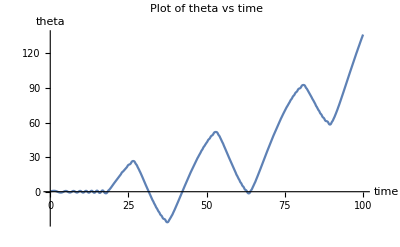

```mathematica
Show[%167,AxesLabel->{HoldForm[time],HoldForm[theta]},PlotLabel->HoldForm[Plot of theta vs time],LabelStyle->{GrayLevel[0],Bold}]
```

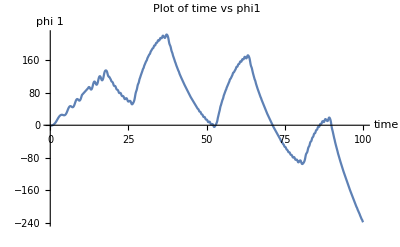

```mathematica
Show[%168,AxesLabel->{HoldForm[time],HoldForm[phi 1]},PlotLabel->HoldForm[Plot of time vs phi1],LabelStyle->{GrayLevel[0],Bold}]
```

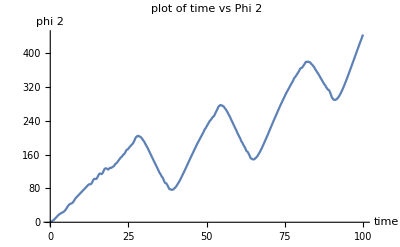

```mathematica
Show[%169,AxesLabel->{HoldForm[time],HoldForm[phi 2]},PlotLabel->HoldForm[plot of time vs Phi 2],LabelStyle->{GrayLevel[0],Bold}]
```